## Introduction

Model with J = - K

## Main

### Equations

#### Defintions

```mathematica
Clear[b,j,k,e,xp,xm,θp,θm];
es={
e-b Cos[xp] Sin[xm],
-b Sin[xp] Cos[xm]-j/2 Sin[2 xm]Cos[2 θm],
e-b Cos[θp] Sin[θm],
-b Sin[θp] Cos[θm]-k/2 Sin[2 θm]Cos[2xm]
}/.j->-k/.b->1;
TableForm[es]
```

e-Cos[xp] Sin[xm]
1/2 k Cos[2 θm] Sin[2 xm]-Cos[xm] Sin[xp]
e-Cos[θp] Sin[θm]
-1/2 k Cos[2 xm] Sin[2 θm]-Cos[θm] Sin[θp]

#### Prepare

```mathematica
tempSub=Solve[es[[{1,3}]]=={0,0},{xm,θm}]/.C[1]->0/.C[2]->0;
TableForm[tempSub]
```

xm→π-ArcSin[e Sec[xp]] | θm→π-ArcSin[e Sec[θp]]
xm→π-ArcSin[e Sec[xp]] | θm→ArcSin[e Sec[θp]]
xm→ArcSin[e Sec[xp]] | θm→π-ArcSin[e Sec[θp]]
xm→ArcSin[e Sec[xp]] | θm→ArcSin[e Sec[θp]]

```mathematica
etemp=(es[[{2,4}]]//TrigExpand)/.tempSub[[4]]//FullSimplify;
TableForm[etemp]
```

-√(1-e^2 Sec[xp]^2) (e k Sec[xp] (-1+2 e^2 Sec[θp]^2)+Sin[xp])
√(1-e^2 Sec[θp]^2) (e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp])

#### Order parameter definition

```mathematica
e3={xp==1/2(x1+x2),xm==1/2(x1-x2),θp==1/2(θ1+θ2),θm==1/2(θ1-θ2)};
sub3=Solve[e3,{x1,x2,θ1,θ2}];
Wp=1/2(Exp[ⅈ(x1+θ1)]+Exp[ⅈ(x2+θ2)]);
Wm=1/2(Exp[ⅈ(x1-θ1)]+Exp[ⅈ(x2-θ2)]);
{Wp,Wm}=({Wp,Wm}/.sub3[[1]])//ExpToTrig//FullSimplify;
Wm=ExpToTrig[Wm]//Simplify;
TableForm[{Wp,Wm}]
```

Cos[xm+θm] (Cos[xp+θp]+ⅈ Sin[xp+θp])
Cos[xm-θm] (Cos[xp-θp]+ⅈ Sin[xp-θp])

### Fixed point 1

#### FP

```mathematica
etemp=(es[[{2,4}]]//TrigExpand)/.tempSub[[4]]//FullSimplify;
etemp//TableForm
e11={etemp[[1,2]],etemp[[2,1]]}//FullSimplify;
TableForm[e11]
fp1=Solve[e11==0,{xp,θp}]//FullSimplify
Length[fp1]
```

-√(1-e^2 Sec[xp]^2) (e k Sec[xp] (-1+2 e^2 Sec[θp]^2)+Sin[xp])
√(1-e^2 Sec[θp]^2) (e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp])

√(1-e^2 Sec[xp]^2)
√(1-e^2 Sec[θp]^2)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{xp→-ArcCos[-e],θp→-ArcCos[-e]},{xp→-ArcCos[-e],θp→ArcCos[-e]},{xp→-ArcCos[-e],θp→-ArcCos[e]},{xp→-ArcCos[-e],θp→ArcCos[e]},{xp→ArcCos[-e],θp→-ArcCos[-e]},{xp→ArcCos[-e],θp→ArcCos[-e]},{xp→ArcCos[-e],θp→-ArcCos[e]},{xp→ArcCos[-e],θp→ArcCos[e]},{xp→-ArcCos[e],θp→-ArcCos[-e]},{xp→-ArcCos[e],θp→ArcCos[-e]},{xp→-ArcCos[e],θp→-ArcCos[e]},{xp→-ArcCos[e],θp→ArcCos[e]},{xp→ArcCos[e],θp→-ArcCos[-e]},{xp→ArcCos[e],θp→ArcCos[-e]},{xp→ArcCos[e],θp→-ArcCos[e]},{xp→ArcCos[e],θp→ArcCos[e]}}

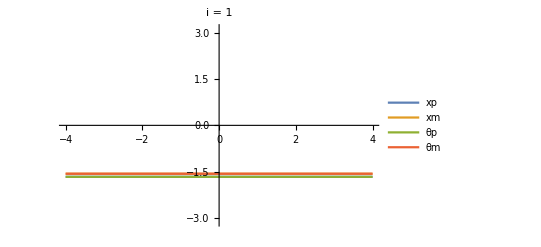
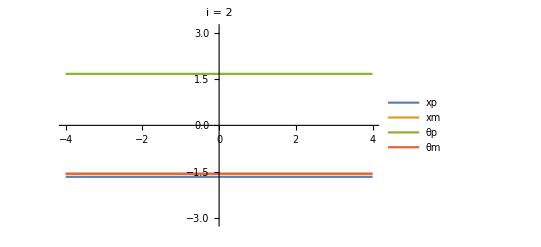
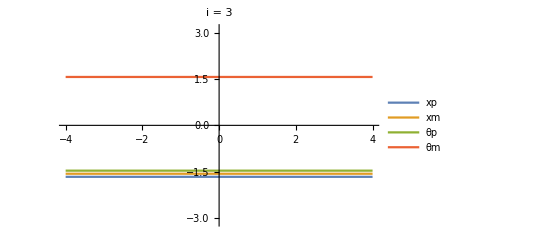
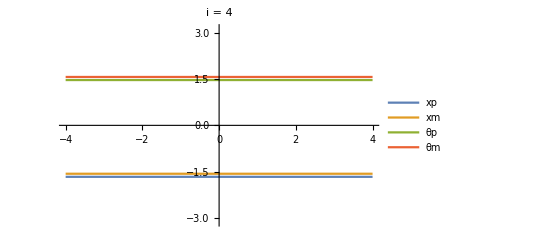
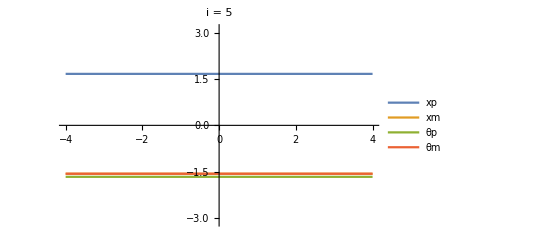
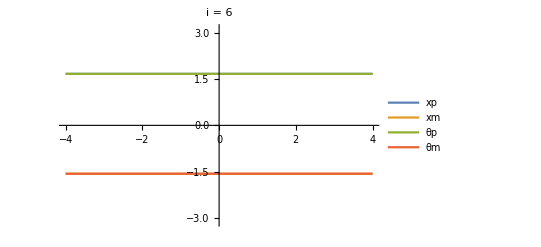
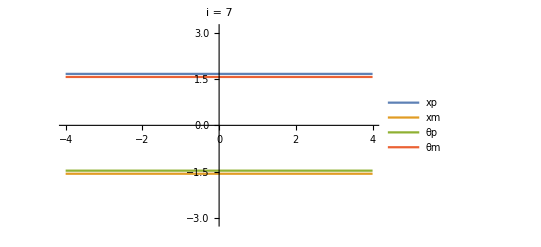
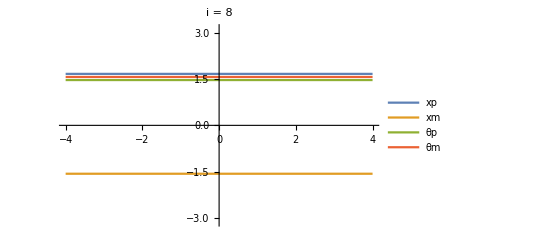

```mathematica
ParallelTable[
Plot[{xp,xm,θp,θm}/.tempSub[[4]]/.fp1[[i]]/.e->0.1//Evaluate,{k,-4,4},PlotRange->{{-4,4},{-π,π}},PlotLegends->{"xp", "xm", "θp", "θm"},LabelStyle->15,PlotLabel->"i = "<>ToString[i]],
{i,1,Length[fp1]}]
```

#### Eigenvalues

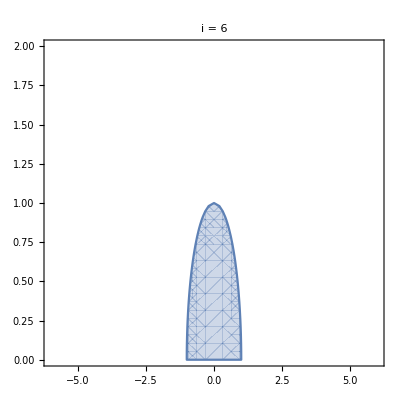
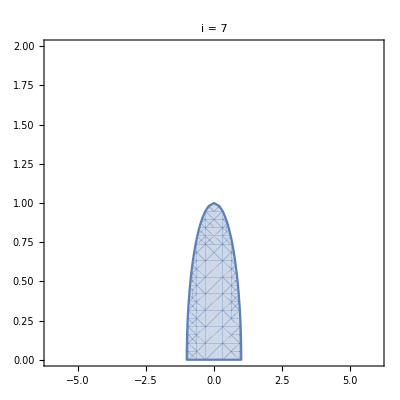
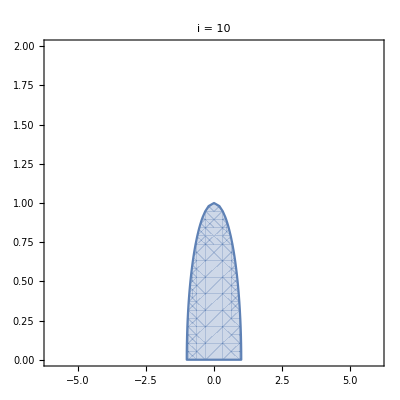
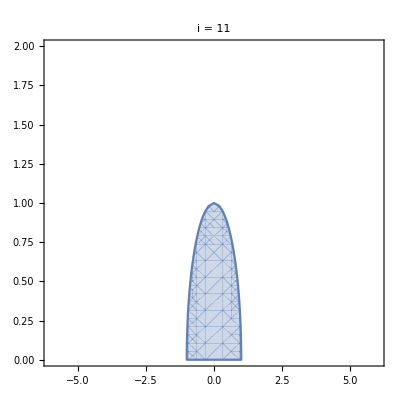
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
$Assumptions={};
ParallelTable[
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp1[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
fixedpoint=({xp,xm,θp,θm}/.tempSub[[4]]/.fp1[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]<=0&&Re[λ[[3]]]<=0&&Re[λ[[4]]]<=0;
RegionPlot[condFixedPointReal&&condLamStable,{k,-6,6},{e,0,2},PlotLabel->"i = "<>ToString[i]],
{i,1,Length[fp1]}
]
```

```mathematica
is={6,7,10,11}
```

```mathematica
i=6;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp1[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
TableForm[λ]
```

-√(1-e^2)
-√(1-e^2)
-√(1-e^2)-k
-√(1-e^2)+k

```mathematica
Solve[λ[[3]]==0,e]//FullSimplify
```

{{e→-√(1-k^2)},{e→√(1-k^2)}}

```mathematica
Solve[λ[[4]]==0,e]//FullSimplify
```

{{e→-√(1-k^2)},{e→√(1-k^2)}}

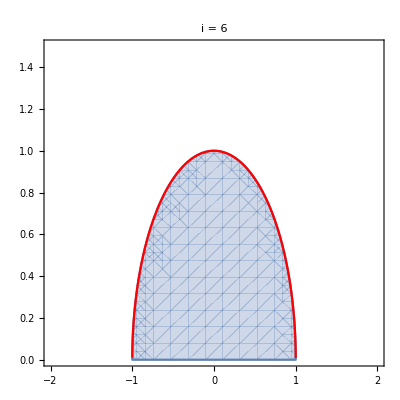

```mathematica
i=6;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp1[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
fixedpoint=({xp,xm,θp,θm}/.tempSub[[4]]/.fp1[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]<=0&&Re[λ[[3]]]<=0&&Re[λ[[4]]]<=0;
p1=RegionPlot[condFixedPointReal&&condLamStable,{k,-2,2},{e,0,1.5},PlotLabel->"i = "<>ToString[i]];
p2=Plot[√(1-k^2),{k,-2,2},PlotStyle->{Red}];
Show[{p1,p2}]
```

#### Order parameter

```mathematica
i=6;
Wp1=(Wp/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp1[[i]]//TrigExpand//FullSimplify;
Wm1=(Wm/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp1[[i]]//TrigExpand//FullSimplify;
TableForm[{Wp1,Wm1}]
```

1-2 e^2+2 ⅈ e √(1-e^2)
1

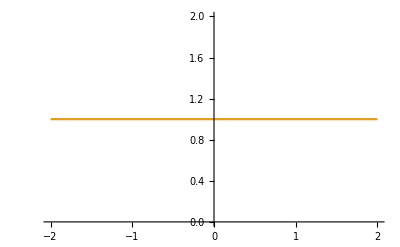

```mathematica
Plot[{Abs[Wp1],Abs[Wm1]},{k,-2,2}]
```

```mathematica
$Assumptions={};
ParallelTable[
Wp1=(Wp/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp1[[i]]//TrigExpand//FullSimplify;
Wm1=(Wm/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp1[[i]]//TrigExpand//FullSimplify;
ContourPlot[{S==Abs[Wp1]/.e->0.1,S==Abs[Wm1]/.e->0.1},{k,-5,5},{S,0,1},PlotLabel->"i = "<>ToString[i],PlotLegends->{"S_+","S_-"},LabelStyle->15],
{i,1,Length[fp1]}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Fixed point 2

#### FP

```mathematica
etemp=(es[[{2,4}]]//TrigExpand)/.tempSub[[4]]//FullSimplify;
etemp//TableForm
e3={etemp[[1,2]],etemp[[2,2]]}//FullSimplify;
TableForm[e3]
fp2=Solve[e3==0,{xp,θp}]//FullSimplify
Length[fp2]
```

-√(1-e^2 Sec[xp]^2) (e k Sec[xp] (-1+2 e^2 Sec[θp]^2)+Sin[xp])
√(1-e^2 Sec[θp]^2) (e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp])

√(1-e^2 Sec[xp]^2)
e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{xp→-ArcCos[-e],θp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[-e],θp→ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[-e],θp→-ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[-e],θp→ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[-e],θp→-ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→-ArcCos[-e],θp→ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→-ArcCos[-e],θp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→-ArcCos[-e],θp→ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→-ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→-ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→-ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→-ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→-ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→-ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]}}

32

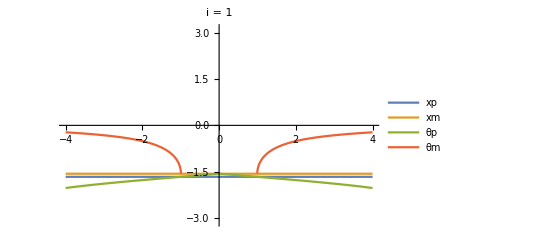
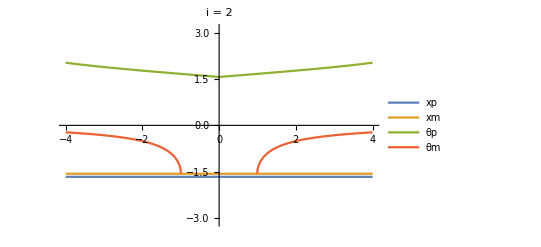
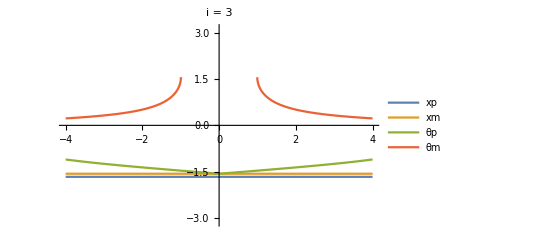
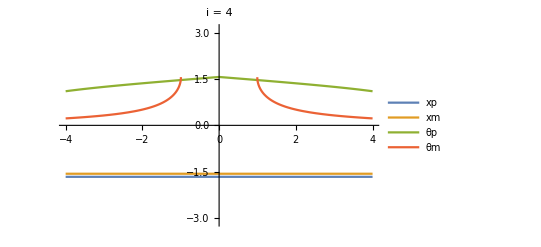
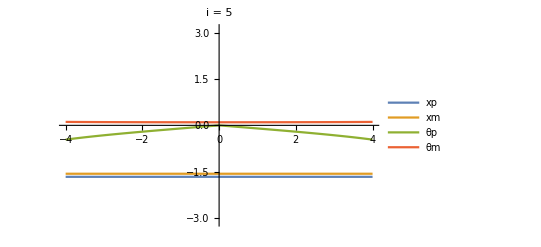
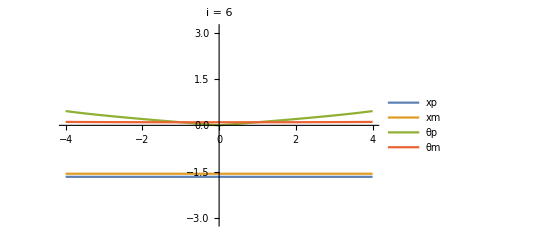
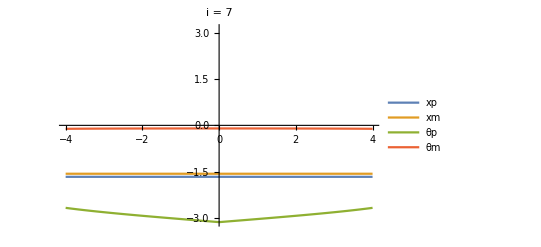
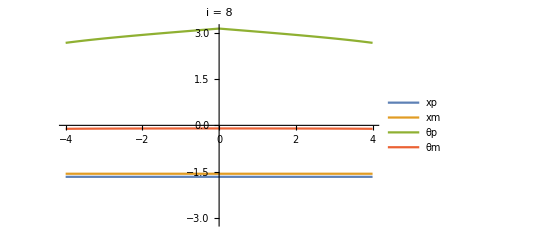

```mathematica
ParallelTable[
Plot[{xp,xm,θp,θm}/.tempSub[[4]]/.fp2[[i]]/.e->0.1//Evaluate,{k,-4,4},PlotRange->{{-4,4},{-π,π}},PlotLegends->{"xp", "xm", "θp", "θm"},LabelStyle->15,PlotLabel->"i = "<>ToString[i]],
{i,1,Length[fp2]}]
```

#### Eigenvalues

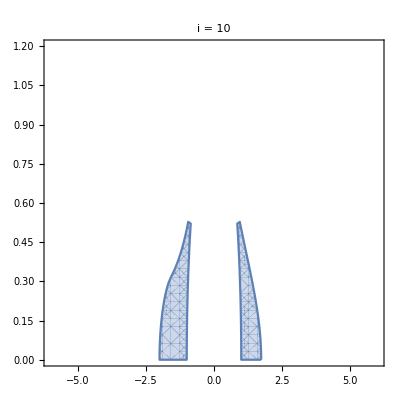
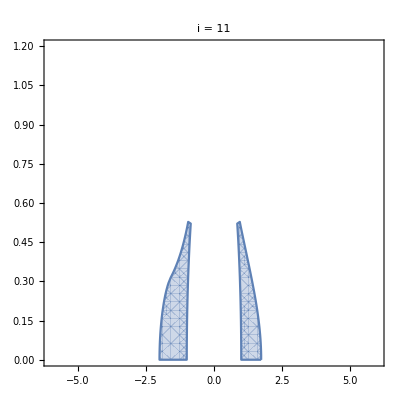
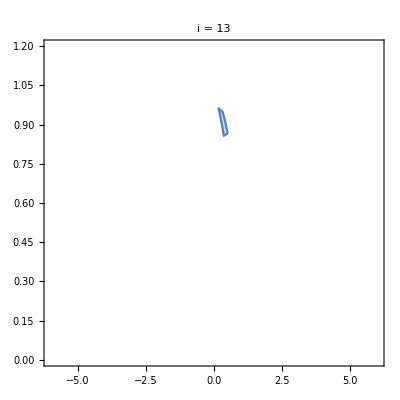
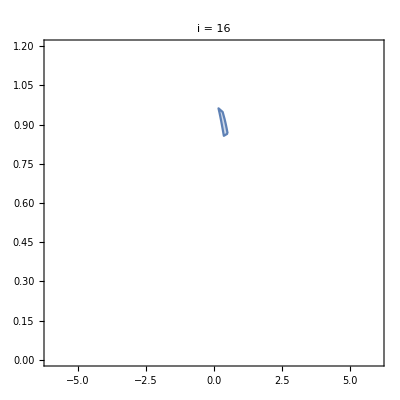
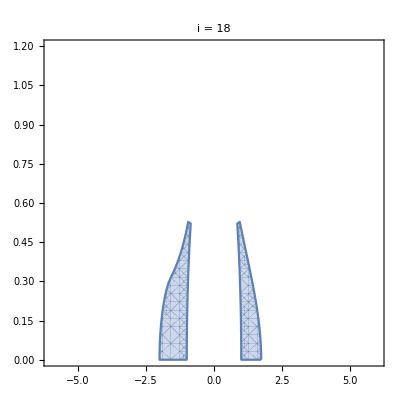
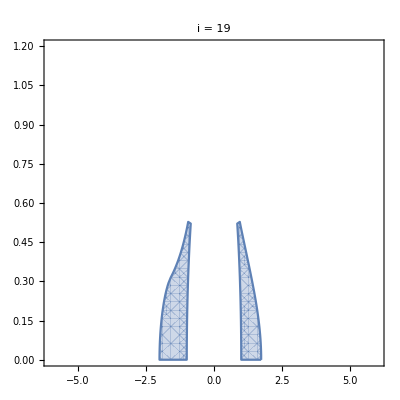
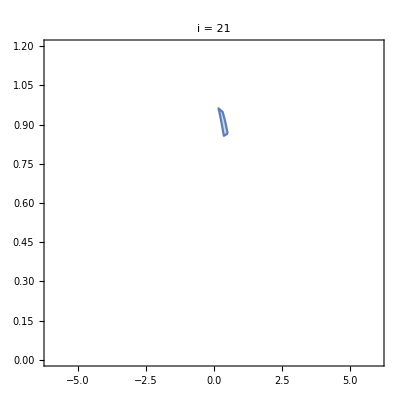
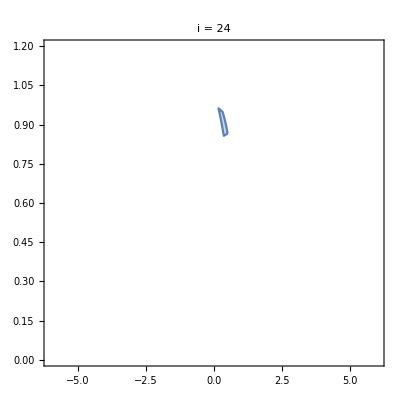
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
$Assumptions={};
ParallelTable[
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp2[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
fixedpoint=({xp,xm,θp,θm}/.tempSub[[4]]/.fp2[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]<=0&&Re[λ[[3]]]<=0&&Re[λ[[4]]]<=0;
RegionPlot[condFixedPointReal&&condLamStable,{k,-6,6},{e,0,1.2},PlotLabel->"i = "<>ToString[i]],
{i,1,Length[fp2]}
]
```

```mathematica
is={10,11,18,19}
```

```mathematica
i=10;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp2[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
TableForm[λ]
```

-√(1-e^2)
(1-k (√(1-e^2)+k)+√(1-4 e^2 k^2))/k
1/2 (k-(2 e √(1+√(1-4 e^2 k^2)))/(√(1-√(1-4 e^2 k^2)))-(1+√(1-4 e^2 k^2)+(√(k^2 (4-4 √(1-4 e^2 k^2)+8 e^2 √(1-4 e^2 k^2)-k^2 (-1+16 e^2+√(1-4 e^2 k^2)))))/(√(1-√(1-4 e^2 k^2))))/k)
1/2 (k-(2 e √(1+√(1-4 e^2 k^2)))/(√(1-√(1-4 e^2 k^2)))-(1+√(1-4 e^2 k^2)-(√(k^2 (4-4 √(1-4 e^2 k^2)+8 e^2 √(1-4 e^2 k^2)-k^2 (-1+16 e^2+√(1-4 e^2 k^2)))))/(√(1-√(1-4 e^2 k^2))))/k)

```mathematica
Solve[λ[[1]]==0,e]
```

{{e→-1},{e→1}}

```mathematica
Solve[λ[[2]]==0,e]
```

{{e→-√(1-k^2)},{e→√(1-k^2)},{e→-(√(-4+5 k^2-k^4))/(3 k)},{e→(√(-4+5 k^2-k^4))/(3 k)}}

```mathematica
Solve[λ[[3]]==0,e]
```

$Aborted

```mathematica
FullSimplify[(√((-3-4 k^2+3 √(1+8 k^2))/k^2))/(2 √2),Assumptions->k>0]
```

(√(-3-4 k^2+3 √(1+8 k^2)))/(2 √2 k)

```mathematica
FullSimplify[k-(2 e √(1+√(1-4 e^2 k^2)))/(√(1-√(1-4 e^2 k^2)))-(1+√(1-4 e^2 k^2)+(√(k^2 (4-4 √(1-4 e^2 k^2)+8 e^2 √(1-4 e^2 k^2)-k^2 (-1+16 e^2+√(1-4 e^2 k^2)))))/(√(1-√(1-4 e^2 k^2))))/k]
```

```mathematica
k-(2 e √(1+√(1-4 e^2 k^2)))/(√(1-√(1-4 e^2 k^2)))-(1+√(1-4 e^2 k^2)+(√(k^2 (4-4 √(1-4 e^2 k^2)+8 e^2 √(1-4 e^2 k^2)-k^2 (-1+16 e^2+√(1-4 e^2 k^2)))))/(√(1-√(1-4 e^2 k^2))))/k
```

```mathematica
temp=FullSimplify[Numerator[Together[λ[[3]]]]]
```

-√(1-√(1-4 e^2 k^2))+k^2 √(1-√(1-4 e^2 k^2))-√(1-4 e^2 k^2) √(1-√(1-4 e^2 k^2))-2 e k √(1+√(1-4 e^2 k^2))-√(k^2 (4-4 √(1-4 e^2 k^2)+8 e^2 √(1-4 e^2 k^2)-k^2 (-1+16 e^2+√(1-4 e^2 k^2))))

```mathematica
removeSqRoot[eqn_,term_]:=Block[{eqn1,Xsol,X},
eqn1=eqn/.term->X;
Xsol=(X/.Solve[eqn1==0,X])[[1]];
Return[Together[Xsol^2-term^2]//Numerator//FullSimplify]
]
```

```mathematica
temp1=removeSqRoot[temp,√(1-√(1-4 e^2 k^2))]
```

4 k (-2 e^2 k^3+k (1-√(1-4 e^2 k^2)+2 e^2 √(1-4 e^2 k^2))+e √(1+√(1-4 e^2 k^2)) √(k^2 (4-4 √(1-4 e^2 k^2)+8 e^2 √(1-4 e^2 k^2)-k^2 (-1+16 e^2+√(1-4 e^2 k^2)))))

```mathematica
temp2=removeSqRoot[temp1,√(k^2 (4-4 √(1-4 e^2 k^2)+8 e^2 √(1-4 e^2 k^2)-k^2 (-1+16 e^2+√(1-4 e^2 k^2))))]
```

2 k^2 (1+8 e^6 k^2-√(1-4 e^2 k^2)+2 e^2 (-1+√(1-4 e^2 k^2)+k^2 (-2+√(1-4 e^2 k^2)))+e^4 (-2-4 √(1-4 e^2 k^2)+4 k^2 (2+√(1-4 e^2 k^2))))

```mathematica
temp3=removeSqRoot[temp2,√(1-4 e^2 k^2)]
```

4 e^4 (-1+2 e k) (1+2 e k) (-1+e^2+k^2) (3 (-1+e^2)+(k+2 e^2 k)^2)

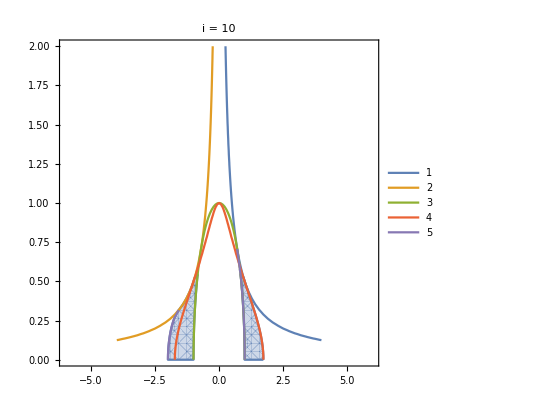

```mathematica
i=10;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp2[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
fixedpoint=({xp,xm,θp,θm}/.tempSub[[4]]/.fp2[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]<=0&&Re[λ[[3]]]<=0&&Re[λ[[4]]]<=0;
p1=RegionPlot[condFixedPointReal&&condLamStable,{k,-6,6},{e,0,2},PlotLabel->"i = "<>ToString[i]];

p2=ContourPlot[{
-1+2 e k==0,
1+2 e k==0,
-1+e^2+k^2==0,
3 (-1+e^2)+(k+2 e^2 k)^2==0,
(1-k (√(1-e^2)+k)+√(1-4 e^2 k^2))/k==0
},{k,-4,4},{e,0,2},FrameLabel->{"K","E"},PlotLegends->Table[i,{i,1,5}]];

Show[{p1,p2}]
```

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

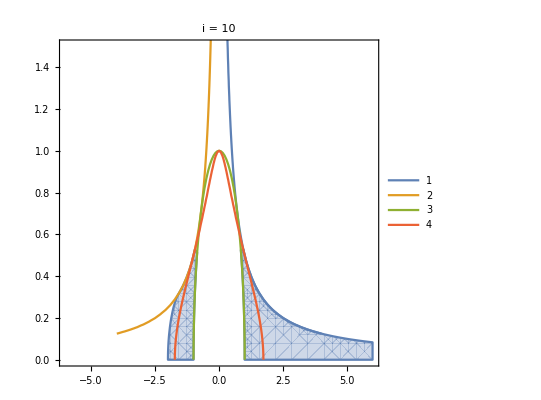

```mathematica
i=10;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp2[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
fixedpoint=({xp,xm,θp,θm}/.tempSub[[4]]/.fp2[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]≤0;
p1=RegionPlot[condFixedPointReal&&condLamStable,{k,-6,6},{e,0,1.5},PlotLabel->"i = "<>ToString[i]];

p2=ContourPlot[{
-1+2 e k==0,
1+2 e k==0,
-1+e^2+k^2==0,
3 (-1+e^2)+(k+2 e^2 k)^2==0
},{k,-4,4},{e,0,2},FrameLabel->{"K","E"},PlotLegends->Table[i,{i,1,4}]];

Show[{p1,p2}]
```

```mathematica
Solve[3 (-1+e^2)+(k+2 e^2 k)^2==0,e]
```

{{e→-(√(-4-3/k^2-(3 √(1+8 k^2))/k^2))/(2 √2)},{e→(√(-4-3/k^2-(3 √(1+8 k^2))/k^2))/(2 √2)},{e→-(√(-4-3/k^2+(3 √(1+8 k^2))/k^2))/(2 √2)},{e→(√(-4-3/k^2+(3 √(1+8 k^2))/k^2))/(2 √2)}}

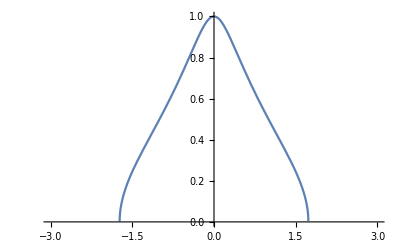

```mathematica
Plot[(√(-4-3/k^2+(3 √(1+8 k^2))/k^2))/(2 √2),{k,-3,3}]
```

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

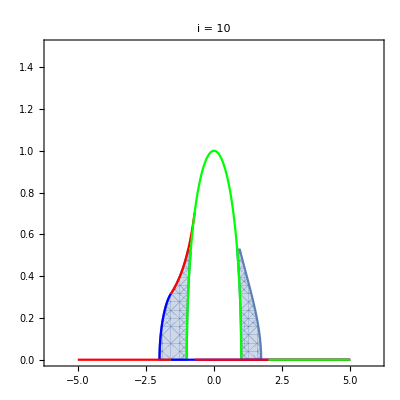

```mathematica
i=10;
k1=-√(5/2);
k2=-1/(√2);
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp2[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
fixedpoint=({xp,xm,θp,θm}/.tempSub[[4]]/.fp2[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]<=0&&Re[λ[[3]]]<=0&&Re[λ[[4]]]<=0;
p1=RegionPlot[condFixedPointReal&&condLamStable,{k,-6,6},{e,0,1.5},PlotLabel->"i = "<>ToString[i]];
p2=Plot[{Piecewise[{{-(√(-4+5 k^2-k^4))/(3 k), k≤k1}, {0, True}}],Piecewise[{{-1/(2k), k1≤k≤k3}, {0, True}}],Piecewise[{{√(1-k^2), k≤2}, {0, True}}]},{k,-5,5},PlotStyle->{Blue,Red,Green}];
Show[{p1,p2}]
```

Ok good.

#### Order parameter

```mathematica
i=10;
Wp2=(Wp/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp2[[i]]//TrigExpand//FullSimplify;
Wm2=(Wm/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp2[[i]]//TrigExpand//FullSimplify;
TableForm[{Wp2,Wm2}]
```

-(e (e-ⅈ √(1-e^2)) (-1+2 ⅈ √(e^2 k^2)+√(1-4 e^2 k^2)))/(-1+√(1-4 e^2 k^2))
(√2 e ⅇ^(-ⅈ (ArcCsc[(√2)/(√(1-√(1-4 e^2 k^2)))]-ArcSin[e])))/(√(1-√(1-4 e^2 k^2)))

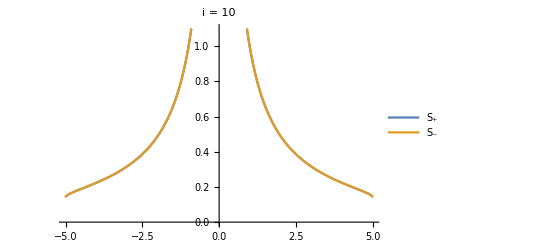
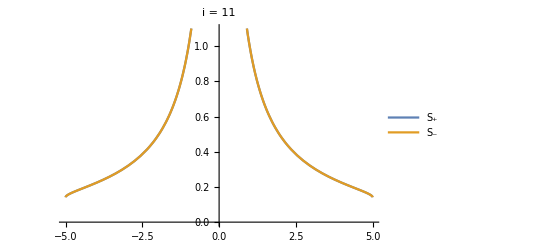
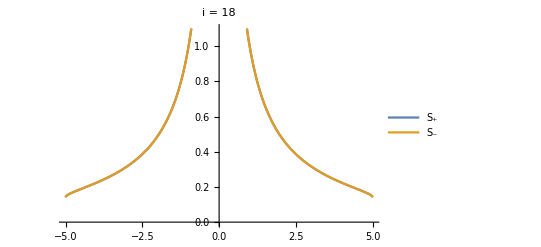
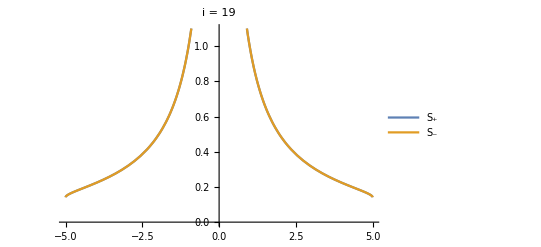

```mathematica
$Assumptions={};
ParallelTable[
Wp2=(Wp/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp2[[i]]//TrigExpand//FullSimplify;
Wm2=(Wm/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp2[[i]]//TrigExpand//FullSimplify;
kc=√(1-e^2)/.e->0.1;
Plot[{Abs[Wp2],Abs[Wm2]}/.e->0.1//Evaluate,{k,-5,5},PlotLabel->"i = "<>ToString[i],PlotLegends->{"S_+","S_-"},LabelStyle->15,PlotRange->{0,1.1}],
{i,{10,11,18,19}}
]
```

### Fixed point 3

#### FP

```mathematica
etemp=(es[[{2,4}]]//TrigExpand)/.tempSub[[4]]//FullSimplify;
etemp//TableForm
e3={etemp[[1,3]],etemp[[2,1]]}//FullSimplify;
TableForm[e3]
fp3=Solve[e3==0,{xp,θp}]//FullSimplify
Length[fp3]
```

-√(1-e^2 Sec[xp]^2) (e k Sec[xp] (-1+2 e^2 Sec[θp]^2)+Sin[xp])
√(1-e^2 Sec[θp]^2) (e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp])

e k Sec[xp] (-1+2 e^2 Sec[θp]^2)+Sin[xp]
√(1-e^2 Sec[θp]^2)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{xp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))],θp→-ArcCos[-e]},{xp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))],θp→ArcCos[-e]},{xp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))],θp→-ArcCos[e]},{xp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))],θp→ArcCos[e]},{xp→ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))],θp→-ArcCos[-e]},{xp→ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))],θp→ArcCos[-e]},{xp→ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))],θp→-ArcCos[e]},{xp→ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))],θp→ArcCos[e]},{xp→-ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))],θp→-ArcCos[-e]},{xp→-ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))],θp→ArcCos[-e]},{xp→-ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))],θp→-ArcCos[e]},{xp→-ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))],θp→ArcCos[e]},{xp→ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))],θp→-ArcCos[-e]},{xp→ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))],θp→ArcCos[-e]},{xp→ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))],θp→-ArcCos[e]},{xp→ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))],θp→ArcCos[e]},{xp→-ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))],θp→-ArcCos[-e]},{xp→-ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))],θp→ArcCos[-e]},{xp→-ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))],θp→-ArcCos[e]},{xp→-ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))],θp→ArcCos[e]},{xp→ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))],θp→-ArcCos[-e]},{xp→ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))],θp→ArcCos[-e]},{xp→ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))],θp→-ArcCos[e]},{xp→ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))],θp→ArcCos[e]},{xp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))],θp→-ArcCos[-e]},{xp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))],θp→ArcCos[-e]},{xp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))],θp→-ArcCos[e]},{xp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))],θp→ArcCos[e]},{xp→ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))],θp→-ArcCos[-e]},{xp→ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))],θp→ArcCos[-e]},{xp→ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))],θp→-ArcCos[e]},{xp→ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))],θp→ArcCos[e]}}

32

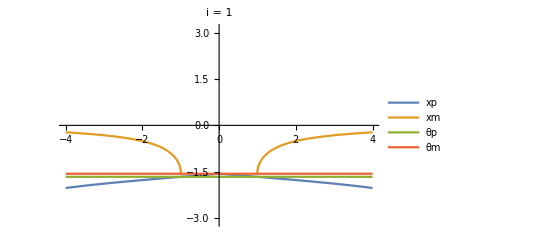
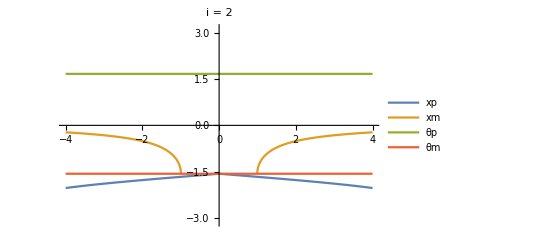
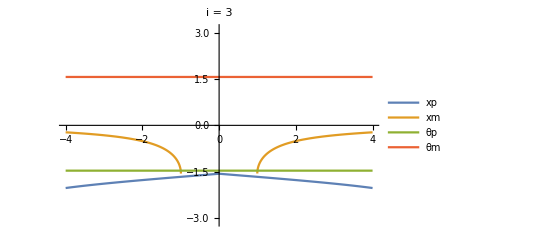
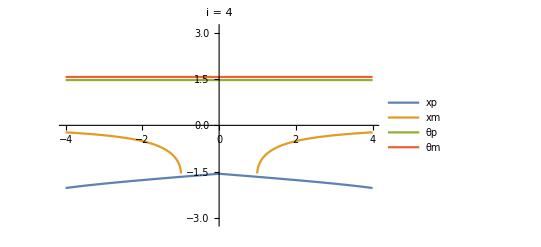
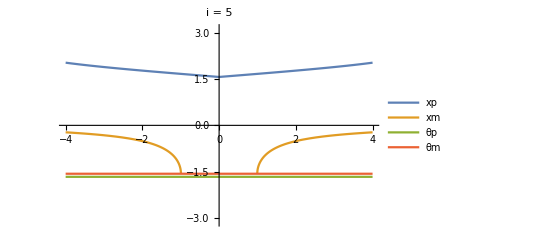
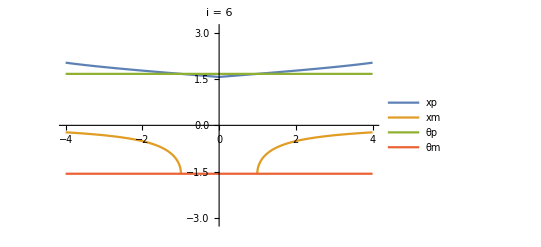
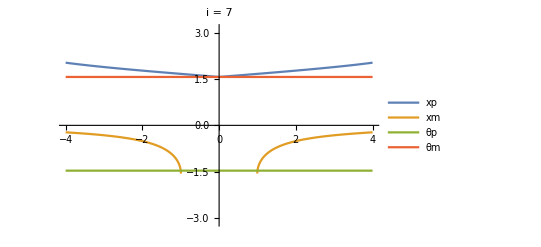
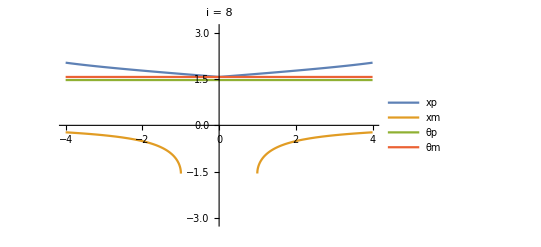

```mathematica
ParallelTable[
Plot[{xp,xm,θp,θm}/.tempSub[[4]]/.fp3[[i]]/.e->0.1//Evaluate,{k,-4,4},PlotRange->{{-4,4},{-π,π}},PlotLegends->{"xp", "xm", "θp", "θm"},LabelStyle->15,PlotLabel->"i = "<>ToString[i]],
{i,1,Length[fp3]}
]
```

#### Eigenvalues

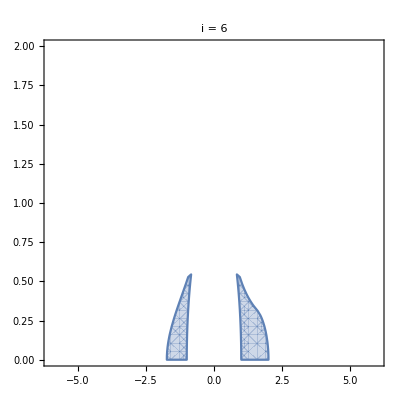
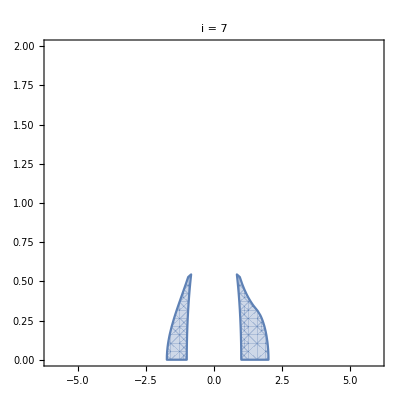
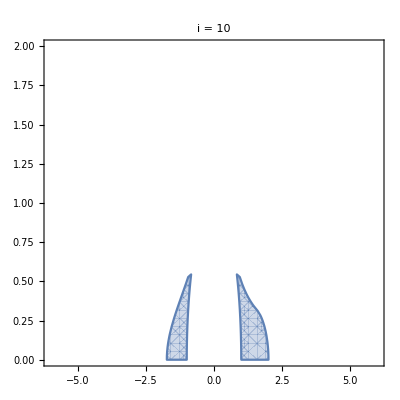
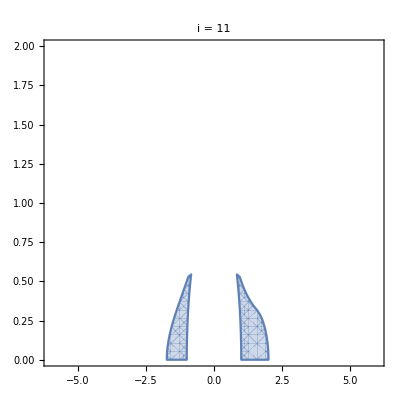
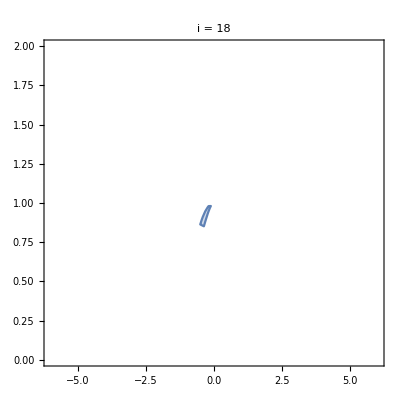
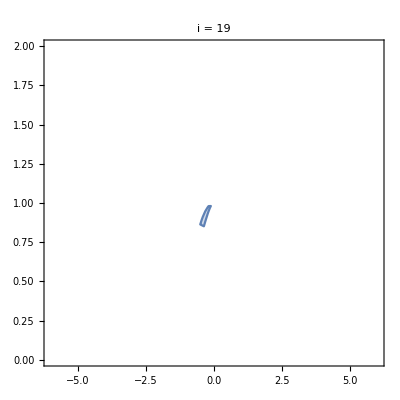
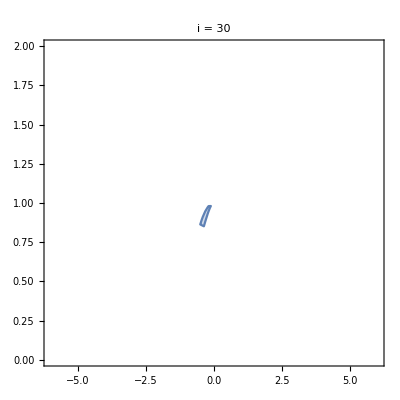
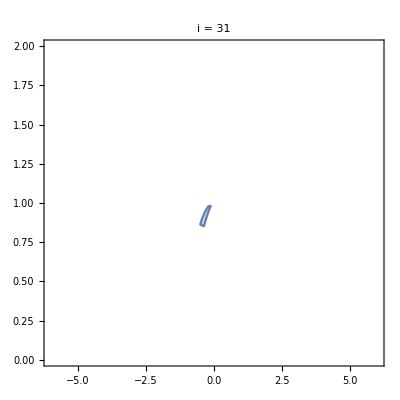
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
$Assumptions={};
ParallelTable[
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp3[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
fixedpoint=({xp,xm,θp,θm}/.tempSub[[4]]/.fp3[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]<=0&&Re[λ[[3]]]<=0&&Re[λ[[4]]]<=0;
RegionPlot[condFixedPointReal&&condLamStable,{k,-6,6},{e,0,2},PlotLabel->"i = "<>ToString[i]],
{i,1,Length[fp3]}
]
```

```mathematica
is={6,7}
```

```mathematica
i=6;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp2[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
TableForm[λ]
```

√(1-e^2)
(-1+k (√(1-e^2)+k)+√(1-4 e^2 k^2))/k
-(1-√(1-4 e^2 k^2)+(-k (2 e √(1-√(1-4 e^2 k^2))+k √(1+√(1-4 e^2 k^2)))+√(k^2 (4+4 √(1-4 e^2 k^2)-8 e^2 √(1-4 e^2 k^2)+k^2 (1-16 e^2+√(1-4 e^2 k^2)))))/(√(1+√(1-4 e^2 k^2))))/(2 k)
1/2 (k+(2 e √(1-√(1-4 e^2 k^2)))/(√(1+√(1-4 e^2 k^2)))+(-1+√(1-4 e^2 k^2)+(√(k^2 (4+4 √(1-4 e^2 k^2)-8 e^2 √(1-4 e^2 k^2)+k^2 (1-16 e^2+√(1-4 e^2 k^2)))))/(√(1+√(1-4 e^2 k^2))))/k)

```mathematica
Solve[-(1+(√(1-e^2)-k) k+√(1-4 e^2 k^2))/k==0,e]//FullSimplify
```

{{e→-√(1-k^2)},{e→√(1-k^2)},{e→-(√(-4+5 k^2-k^4))/(3 k)},{e→(√(-4+5 k^2-k^4))/(3 k)}}

```mathematica
λ[[2]]
```

-(1+(√(1-e^2)-k) k+√(1-4 e^2 k^2))/k

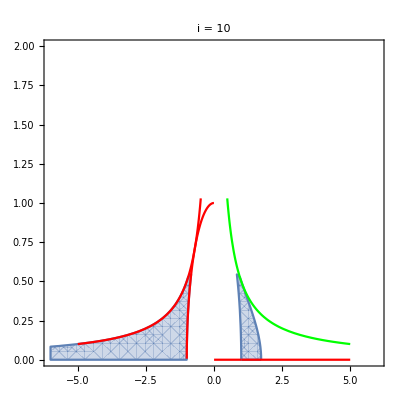

```mathematica
i=10;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp2[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
fixedpoint=({xp,xm,θp,θm}/.tempSub[[4]]/.fp2[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]<=0&&Re[λ[[3]]]<=0&&Re[λ[[4]]]<=0;
p1=RegionPlot[condFixedPointReal&&condLamStable,{k,-6,6},{e,0,2},PlotLabel->"i = "<>ToString[i]];
p2=Plot[{-1/(2k),√(1-k^2)HeavisideTheta[-k],1/(2k)},{k,-5,5},PlotStyle->{Red,Red,Green}];
Show[{p1,p2}]
```

#### Order parameter

```mathematica
is={6,7,10,11,18,19}
```

{6,7,10,11,18,19}

```mathematica
i=19;
Wp3=(Wp/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp3[[i]]//TrigExpand//FullSimplify;
Wm3=(Wm/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp3[[i]]//TrigExpand//FullSimplify;
TableForm[{Wp2,Wm2}]
```

-(e (e-ⅈ √(1-e^2)) (-1+2 ⅈ √(e^2 k^2)+√(1-4 e^2 k^2)))/(-1+√(1-4 e^2 k^2))
(√2 e ⅇ^(-ⅈ (ArcCsc[(√2)/(√(1-√(1-4 e^2 k^2)))]-ArcSin[e])))/(√(1-√(1-4 e^2 k^2)))

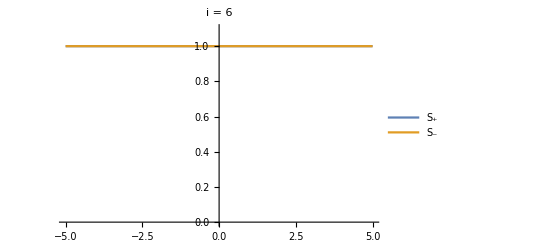
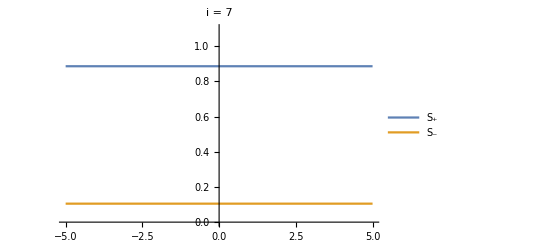

```mathematica
$Assumptions={};
ParallelTable[
Wp3=(Wp/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp3[[i]]//TrigExpand//FullSimplify;
Wm3=(Wm/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp3[[i]]//TrigExpand//FullSimplify;
Plot[{Abs[Wp3],Abs[Wm3]}/.e->e1//Evaluate,{k,-5,5},PlotLabel->"i = "<>ToString[i],PlotLegends->{"S_+","S_-"},LabelStyle->15,PlotRange->{0,1.1}],
{i,{6,7}}
]
```

```mathematica
$Assumptions={0≤e≤1,k∈Reals};
Abs[Wp3]//ComplexExpand//FullSimplify
```

Piecewise[{{(√2 e)/(√(1-√(1-4 e^2 k^2))), 4 e^2 k^2≤1}, {e/(√(e k (2 e k+√(-1+4 e^2 k^2)))), k<0&&4 e^2 k^2>1}, {√((e (2 e k+√(-1+4 e^2 k^2)))/k), True}}]

### Fixed point 4

#### FP

```mathematica
etemp=(es[[{2,4}]]//TrigExpand)/.tempSub[[4]]//FullSimplify;
etemp//TableForm
e4={etemp[[1,3]],etemp[[2,2]]}//FullSimplify;
TableForm[e4]
fp4=Solve[e4==0,{xp,θp}]//FullSimplify
Length[fp4]
```

-√(1-e^2 Sec[xp]^2) (e k Sec[xp] (-1+2 e^2 Sec[θp]^2)+Sin[xp])
√(1-e^2 Sec[θp]^2) (e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp])

e k Sec[xp] (-1+2 e^2 Sec[θp]^2)+Sin[xp]
e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp]

#### FP solve by hand

```mathematica
et1=e4[[1]]
```

e k Sec[xp] (-1+2 e^2 Sec[θp]^2)+Sin[xp]

```mathematica
Solve[et1==0,Sec[θp]]
```

{{Sec[θp]→-(√(e k-Cos[xp] Sin[xp]))/(√2 e^(3/2) √k)},{Sec[θp]→(√(e k-Cos[xp] Sin[xp]))/(√2 e^(3/2) √k)}}

I’ve worked out sin θ=1/(√(1-1/(sec^2 θ)))

```mathematica
sub={Sec[θp]->(√(e k-Cos[xp] Sin[xp]))/(√2 e^(3/2) √k),Sin[θp]->√(1-(1/((√(e k-Cos[xp] Sin[xp]))/(√2 e^(3/2) √k)))^2)};
```

```mathematica
et2=FullSimplify[Numerator[Together[e4[[2]]/.sub]]]
```

-√k √(2 e k-Sin[2 xp])+2 e^2 √k Sec[xp]^2 √(2 e k-Sin[2 xp])-2 √e √(1+(4 e^3 k)/(-2 e k+Sin[2 xp]))

```mathematica
removeSqRoot[eqn_,term_]:=Block[{eqn1,Xsol,X},
eqn1=eqn/.term->X;
Xsol=(X/.Solve[eqn1==0,X])[[1]];
Return[Together[Xsol^2-term^2]//Numerator]
]
```

```mathematica
et3=removeSqRoot[et2,√(1+(4 e^3 k)/(-2 e k+Sin[2 xp]))]//TrigExpand
```

-k/8+(e^2 k^3)/2-1/8 k Cos[xp]^2+1/2 e^2 k Cos[xp]^2-1/32 k Cos[xp]^4+1/8 k Sec[xp]^2-9/2 e^2 k Sec[xp]^2+8 e^4 k Sec[xp]^2+2 e^2 k^3 Sec[xp]^2-8 e^4 k^3 Sec[xp]^2+5/32 k Sec[xp]^4-4 e^2 k Sec[xp]^4+8 e^4 k Sec[xp]^4+3/2 e^2 k^3 Sec[xp]^4-8 e^4 k^3 Sec[xp]^4+16 e^6 k^3 Sec[xp]^4+3/2 e Cos[xp] Sin[xp]-3/2 e k^2 Cos[xp] Sin[xp]+15/8 k Sin[xp]^2-15/2 e^2 k Sin[xp]^2+7/8 k Cos[xp]^2 Sin[xp]^2-35/16 k Sin[xp]^4+4 e Tan[xp]-4 e k^2 Tan[xp]+16 e^3 k^2 Tan[xp]+5/2 e Sec[xp]^2 Tan[xp]-5/2 e k^2 Sec[xp]^2 Tan[xp]+16 e^3 k^2 Sec[xp]^2 Tan[xp]-32 e^5 k^2 Sec[xp]^2 Tan[xp]-5 e Sin[xp]^2 Tan[xp]+5 e k^2 Sin[xp]^2 Tan[xp]+3/4 k Tan[xp]^2-3 e^2 k^3 Tan[xp]^2-1/8 k Sec[xp]^2 Tan[xp]^2+9/2 e^2 k Sec[xp]^2 Tan[xp]^2-8 e^4 k Sec[xp]^2 Tan[xp]^2-2 e^2 k^3 Sec[xp]^2 Tan[xp]^2+8 e^4 k^3 Sec[xp]^2 Tan[xp]^2-15/8 k Sin[xp]^2 Tan[xp]^2+15/2 e^2 k Sin[xp]^2 Tan[xp]^2+7/8 k Sin[xp]^4 Tan[xp]^2-4 e Tan[xp]^3+4 e k^2 Tan[xp]^3-16 e^3 k^2 Tan[xp]^3+3/2 e Sin[xp]^2 Tan[xp]^3-3/2 e k^2 Sin[xp]^2 Tan[xp]^3-1/8 k Tan[xp]^4+1/2 e^2 k^3 Tan[xp]^4+1/8 k Sin[xp]^2 Tan[xp]^4-1/2 e^2 k Sin[xp]^2 Tan[xp]^4-1/32 k Sin[xp]^4 Tan[xp]^4

```mathematica
sub2={Cos[xp]->c,Sec[xp]->1/c,Tan[xp]->(√(1-c^2))/c,Sin[xp]->√(1-c^2)};
et4=FullSimplify[Numerator[et3/.sub2//Simplify]][[2]]//FullSimplify
```

c^8 k-8 c^3 √(1-c^2) e^3 k^2+8 c √(1-c^2) e^5 k^2-4 e^6 k^3-c^6 (k+4 e^2 k)-c^4 e^2 k (-6+k^2)+2 c^5 √(1-c^2) e (-1+k^2)+4 c^2 e^4 k (-1+k^2)

```mathematica
et5=removeSqRoot[et4,√(1-c^2)]//FullSimplify
```

(c^6 (-1+c^2)+e^2 (c^2-2 e^2)^2 k^2) (4 c^4 e^2+c^2 (c^6-8 e^4-c^4 (1+8 e^2)+4 c^2 (e^2+4 e^4)) k^2+e^2 (c^2-2 e^2)^2 k^4)

I think these are clean polynomials in c^2....

```mathematica
et6=et5/.c->√c1//FullSimplify
```

((-1+c1) c1^3+e^2 (c1-2 e^2)^2 k^2) (4 c1^2 e^2+c1 ((-1+c1) c1^2+4 (1-2 c1) c1 e^2+8 (-1+2 c1) e^4) k^2+e^2 (c1-2 e^2)^2 k^4)

```mathematica
Collect[et6[[1]],c1]
```

-c1^3+c1^4+c1^2 e^2 k^2-4 c1 e^4 k^2+4 e^6 k^2

```mathematica
Collect[et6[[2]],c1]
```

c1^4 k^2+4 e^6 k^4+c1^3 (-k^2-8 e^2 k^2)+c1^2 (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)+c1 (-8 e^4 k^2-4 e^4 k^4)

Yes, a cubic and a quartic in c1 = c^2. So they have known, but ugly, solutions. Nice!! In principle I’m done. Just gotta fold back

```mathematica
fp4sub=Solve[et5==0,c];
Length[fp4sub]
fp4sub
```

16

{{c→-√(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→√(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→-√(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→√(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→-√(1/4+2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2+(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→√(1/4+2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2+(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→-√(1/4+2 e^2+(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2+(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→√(1/4+2 e^2+(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2+(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→-√(1/4-1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)-(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→√(1/4-1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)-(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→-√(1/4-1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)-(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→√(1/4-1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)-(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→-√(1/4+1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)+(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→√(1/4+1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)+(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→-√(1/4+1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)+(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→√(1/4+1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)+(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))}}

#### Collect

```mathematica
Clear[k,e]
fp4=Table[{xp->ArcCos[c],xm->ArcSin[e Sec[xp]]/.xp->ArcCos[c],θp->ArcCos[((√2 e^(3/2) √k)/(√(-c √(1-c^2)+e k)))],θm->ArcSin[e Sec[θp]]/.θp->ArcCos[((√2 e^(3/2) √k)/(√(-c √(1-c^2)+e k)))]}/.fp4sub[[i]],{i,1,Length[fp4sub]}];
```

```mathematica
i=3;
Wp4=(Wp//TrigExpand)/.fp4[[i]]//Simplify;
Wm4=(Wm//TrigExpand)/.fp4[[i]]//Simplify;
```

```mathematica
i=8;
Wp4=(Wp//TrigExpand)/.fp4[[i]]//Simplify;
Wm4=(Wm//TrigExpand)/.fp4[[i]]//Simplify;
```

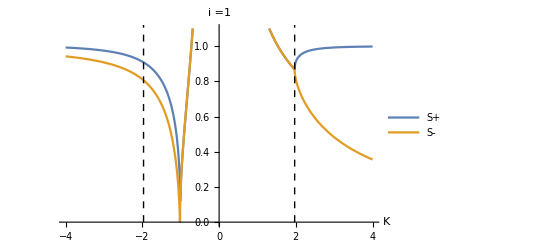
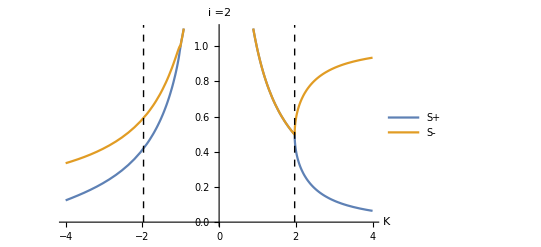
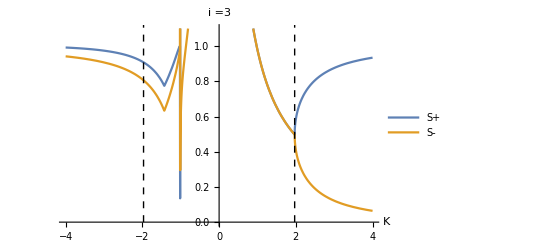
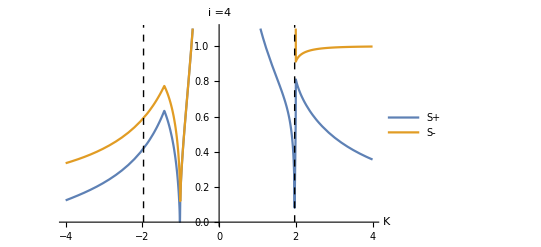
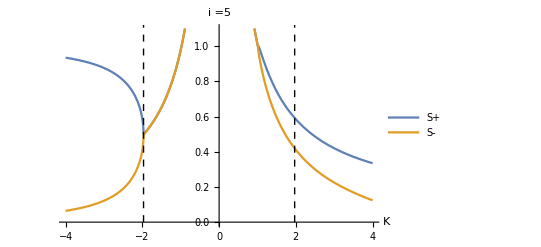
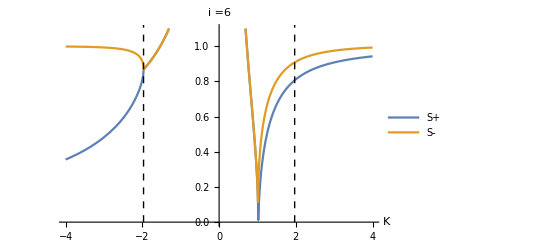
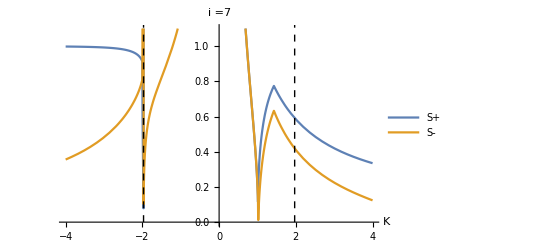
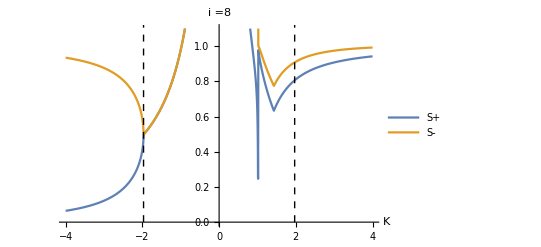
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelTable[
Wp4=(Wp//TrigExpand)/.fp4[[i]];
Wm4=(Wm//TrigExpand)/.fp4[[i]];
e1=0.1;
Plot[{Abs[Wp4/.e->e1],Abs[Wm4/.e->e1]},{k,-4,4},PlotRange->{0,1.1},AxesLabel->{"K"},LabelStyle->15,PlotLabel->"i ="<>ToString[i],PlotLegends->{"S+","S-"},Epilog->{
Black,Dashed,
Line[{{-1.9694507563684027,0},{-1.9694507563684027,2}}],
Line[{{1.9694507563684027,0},{1.9694507563684027,2}}]
}],
{i,1,Length[fp4]}
]
```

Plot versus E

```mathematica
ParallelTable[
Wp4=(Wp//TrigExpand)/.fp4[[i]];
Wm4=(Wm//TrigExpand)/.fp4[[i]];
e1=0.1;
Plot[{Abs[Wp4/.k->3],Abs[Wm4/.k->3]},{e,0,5},PlotRange->{0,1.1},AxesLabel->{"E"},LabelStyle->15,PlotLabel->"i ="<>ToString[i],PlotLegends->{"S+","S-"},Epilog->{
Black,Dashed,
Line[{{-1.9694507563684027,0},{-1.9694507563684027,2}}],
Line[{{1.9694507563684027,0},{1.9694507563684027,2}}]
}],
{i,1,Length[fp4]}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
i=3;
Wp4=(Wp//TrigExpand)/.fp4[[i]];
Wm4=(Wm//TrigExpand)/.fp4[[i]];
```

```mathematica
$Assumptions={{e,k}∈Reals};
ComplexExpand[Abs[Wp4],TargetFunctions->{Re, Im}]
```

√((1)^2+((e^2 Cos[1/2 ArcTan[1]] Cos[1/2 ArcTan[1/4+3+1/2 Cos[1/2 1] (1)^(1/4),1]] ((1)^2+(1)^2)^(1/4))/(((1/4+3+1)^2+(1)^2)^(1/4))+1/1+10+1+(1^2/(4 e^2 k^2)+(1-1)^2)^(1/4) Sin[1/2 ArcTan[1-1/(2 e k),-1/(2 e k)]] (1))^2)
 |  |  |  |

```mathematica
p2=ContourPlot[2+64 e^4-(2 √(-16 e^2+k^2))/k-(8 e^2 (2-2 k^2+k^4+2 k √(-16 e^2+k^2)-k^3 √(-16 e^2+k^2)))/k^2==0,{k,-4,4},{e,0,1.5}]
```

-Graphics-

```mathematica
p3=Plot[1/2 √(1-1/k^2+(√(-4+k^2))/k),{k,-4,4}];
Show[{pfinal,p3}]
```

-Graphics-

#### Plot

```mathematica
ParallelTable[
Plot[{xp,xm,θp,θm}/.fp4[[i]]/.e->0.1//Evaluate,{k,-4,4},PlotRange->{{-4,4},{-π,π}},PlotLegends->{"xp", "xm", "θp", "θm"},LabelStyle->15,PlotLabel->"i = "<>ToString[i]],
{i,1,Length[fp4]}
]
```

General::munfl: ArcSin[0.509205-1.35902×10^-16 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcSin[0.509205-1.44246×10^-16 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcCos[-0.901507+1.60399×10^-20 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcCos[0.901507+5.52014×10^-17 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcSin[0.509205-1.35902×10^-16 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: ArcSin[0.808364-4.9498×10^-17 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcCos[0.901507-1.60399×10^-20 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Eigenvalues

```mathematica
$Assumptions={};
ParallelTable[
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.fp4[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
fixedpoint=({xp,xm,θp,θm}/.fp4[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]<=0&&Re[λ[[3]]]<=0&&Re[λ[[4]]]<=0;
RegionPlot[condFixedPointReal&&condLamStable,{k,-4,3},{e,0,2},PlotLabel->"i = "<>ToString[i]],
{i,1,2}
]
```

$Aborted

```mathematica
i=3;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.fp4[[i]];
λ=Eigenvalues[J1];
TableForm[λ]
```

$Aborted

```mathematica
i=3;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=Simplify[TrigExpand[J]/.fp4[[i]]];
Print["Starting eigenvalues"]
λ=Eigenvalues[J1]
```

$Aborted

```mathematica
ParallelTable[
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]};
J1=Simplify[TrigExpand[J]/.fp4[[i]]/.{k->-1,e->0.1}];
λ=Eigenvalues[J1];
cond=Re[λ[[1]]]<0&&Re[λ[[2]]]<0&&Re[λ[[3]]]<0&&Re[λ[[4]]]<0;
cond,
{i,1,Length[fp4]}
]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

Must be some other branch then

#### Order parameter

```mathematica
ParallelTable[
Wp4=(Wp//TrigExpand)/.fp4[[i]];
Wm4=(Wm//TrigExpand)/.fp4[[i]];
e1=0.1;
Plot[{Abs[Wp4/.e->e1],Abs[Wm4/.e->e1]},{k,-4,4},PlotRange->{0,1.1},AxesLabel->{"K"},LabelStyle->15,PlotLabel->"i ="<>ToString[i],PlotLegends->{"S+","S-"},Epilog->{
Black,Dashed,
Line[{{-1.9694507563684027,0},{-1.9694507563684027,2}}],
Line[{{1.9694507563684027,0},{1.9694507563684027,2}}]
}],
{i,1,Length[fp4]}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Bifurcation diagram

### Version 1

```mathematica
k1=-√(5/2);
k2=-1/(√2);

(*Main template*)
{kmin,kmax}={-3,3};
p1=Plot[0,{k,kmin,kmax},AxesLabel->{Style["K",Italic,20],Style["E",Italic,20]},PlotStyle->{White},PlotRange->{Automatic,{0,1.2}},TicksStyle->13,
Epilog->{
Text[Style["1",18],{0.35,0.5}],
Text[Style["2,3",18],{-1.4,0.15}],
Text[Style["??",16],{-1.5,0.8}],
Text[Style["2,3",18],{1.4,0.15}],
Text[Style["4",16],{-2.5,0.15}],
Text[Style["4",16],{2.5,0.15}],
(*Text[Style["1,2,3",18],{1.3,0.15}],*)
(*Text[Style["SNIPER",Blue,14],{0.35,1.075}],
Text[Style["SNIPER",Blue,14],{-1.6,0.43}],
Text[Style["SN",Blue,14],{-0.75,0.2}],*)
(*Text[Style["SN",Blue,14],{0.75,0.2}],
Text[Style["SN",Blue,14],{1.5,0.4}],*)
PointSize[Large],Point[{-1/(√2),1/(√2)}],
PointSize[Large],Point[{1/(√2),1/(√2)}]
}];

(*FP1 + FP2*)
p2=Plot[-(√(-4+5 k^2-k^4))/(3 k),{k,-3,k1},PlotStyle->Black];
p3=Plot[-1/(2k),{k,k1,k2},PlotStyle->Black];
p4=Plot[√(1-k^2),{k,kmin,kmax},PlotStyle->Black];

p5=Plot[(√(-4+5 k^2-k^4))/(3 k),{k,-k1,3},PlotStyle->Black];
p6=Plot[1/(2k),{k,-k1,-k2},PlotStyle->Black];

pfinal=Show[{p1,p2,p3,p4,p5,p6}]
```

-Graphics-

### Version 3

```mathematica
curve1=√(1-e^2)-k;
curve2=1+2 e k;
curve3=e-(√(-3-4 k^2+3 √(1+8 k^2)))/(2 √2 k);
kc1=1/(√2);
kc2=√(1/2 (3-√3));
p1=Plot[{
(*Monostable region: FP1*)
√(1-k^2),

(*Bistable region: FP2 + FP3*)
√(1-k^2)HeavisideTheta[-k],-1/(2 k)HeavisideTheta[-k-kc1],
},{k,-3,2},AxesLabel->{Style["K",Italic,20],Style["E",Italic,20]},PlotStyle->{Black,Black,Black,Black},PlotRange->{Automatic,{0,1.2}},TicksStyle->13,
Epilog->{
Text[Style["FP1",15],{0.35,0.5}],
Text[Style["FP2 + FP3",15],{-1.7,0.125}],
Text[Style["periodic",16],{-1.5,0.8}],
(*Text[Style["1,2,3",18],{1.3,0.15}],*)
Text[Style["SNIPER",Blue,14],{0.35,1.075}],
Text[Style["SNIPER",Blue,14],{-1.6,0.43}],
Text[Style["SN",Blue,14],{-0.75,0.2}],
(*Text[Style["SN",Blue,14],{0.75,0.2}],
Text[Style["SN",Blue,14],{1.5,0.4}],*)
PointSize[Large],Point[{-1/(√2),1/(√2)}]
}
]

SetDirectory[NotebookDirectory[]];
Export["figures/bif-diagram-J-K.png",p1];
```

-Graphics-

Notice there is a co-dimension two SNIPER-SADDLE point at (K,E) ={-1/(√2),1/(√2)}].